# Electric Field Plots

```mathematica
dipole=1/(√(x^2+(-y-1/2)^2))-1/(√(x^2+(1/2-y)^2));
```

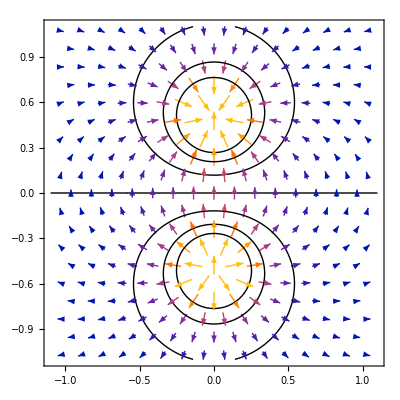

```mathematica
PotentialElectricFieldPlot[dipole,
{x,1.1,-1.1},{y,1.1,-1.1}]
```

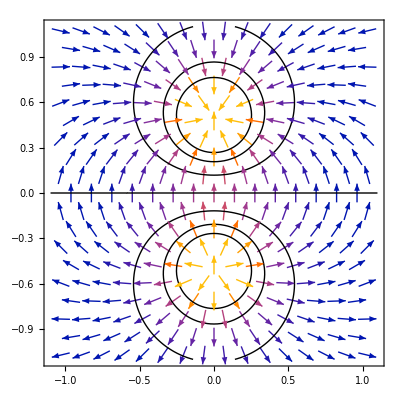

```mathematica
PotentialElectricFieldPlot[dipole,
{x,1.1,-1.1},{y,1.1,-1.1},VectorScaling->None]
```

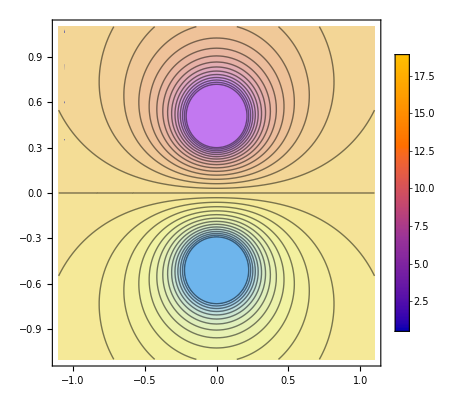

```mathematica
PotentialElectricFieldPlot[
dipole,
{x,-1.1,1.1},
{y,-1.1,1.1},
ContourShading->Automatic,
PlotRange->Automatic,
ColorFunction->"Pastel",
ClippingStyle->Automatic,
Contours->30,
PlotLegends->Automatic
]
```

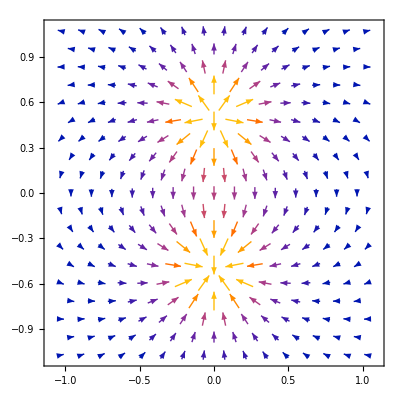

```mathematica
GradientFieldPlot[dipole,{x,-1.1,1.1},{y,-1.1,1.1}]
```